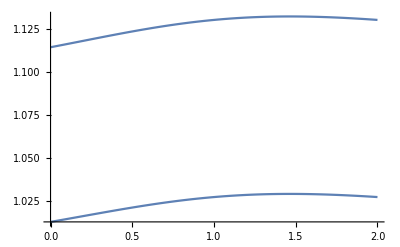

```mathematica
SetOptions[EvaluationNotebook[],CellContext->Notebook]
SetDirectory[NotebookDirectory[]];
Needs["gUtils`"];
Needs["gBRDF`"];
Needs["sgCommon`"];
Needs["gPlots`"];
Needs["gPlots3D`"];
Needs["gSphericalCap`"];

representPt={2,1};
groundPt={0,0};
lightPt={-1,1};
viewDir[wallY_]:=Normalize[groundPt-{2,wallY}];
lightDir[wallY_]:=Normalize[lightPt-{2,wallY}];
halfDir[wallY_]:=Normalize[(viewDir[wallY]+lightDir[wallY])/2];
p1=Plot[1/Dot[halfDir[wallY],viewDir[wallY]],{wallY,0,2}];
p2=Plot[1.1/Dot[halfDir[wallY],viewDir[wallY]],{wallY,0,2}];
Show[p1,p2,PlotRange->All]
```

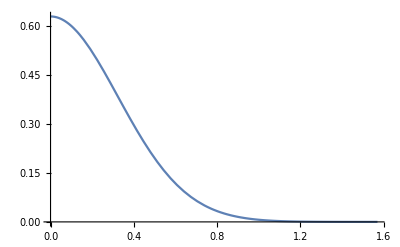

```mathematica
testProductIntegral[{inP1_,λ1_,μ1_},{inP2_,λ2_,μ2_},dotP_]:=Module[
	{p1,p2,λ3,c1,c2},
	p1=Normalize[inP1];
	p2=Normalize[inP2];
	
	c1=λ1*λ2/(λ1+λ2);
	(*c2=Dot[p1,p2];*)	
c2=dotP;
	λ3=λ1+λ2-c1*(1-c2);
	
	μ1*μ2*(2π)/λ3 Exp[c1*(c2-1)]
];

testProduct[{p1_,λ1_,μ1_},{p2_,λ2_,μ2_},dotP_]:=Module[
	{p3,λ3,μ3},
	
	λ3=(λ1+λ2)-(λ1*λ2/(λ1+λ2))*(1-dotP);
	p3=(λ1*p1+λ2*p2)/λ3;
	μ3=Exp[λ3-(λ1+λ2)];
	
	{p3,λ3,μ3}
];

sg3=testProductIntegral[{{1,1,1},λ1,μ1},{{-1,-1,1},λ2/VoH,μ2},VoL];
sg31=sg3/.{λ1->5,λ2->5,μ1->1,μ2->1};
Plot3D[sg31,{VoL,0,1},{VoH,0,1}];
(*sg32=sg31/.{VoL->Cos[2θ],VoH->Cos[θ+x]};
sg33=sg32/.{θ->π/8};
p31=Plot[sg33,{x,-3π/4,π/4}];*)
sg32=sg31/.{VoL->Cos[2θ],VoH->Cos[θ]};
p31=Plot[sg32,{θ,0,π/2}]

sg3a=sg3/.{μ1->1,μ2->1};
sg3b=sg3a/.{VoL->(2Cos[θ]^2-1),VoH->Cos[θ]};
```

```mathematica
sg4a[λ1_,λ2_,θ_]:=Block[{},(λ1 λ2 (-2+2 Cos[θ]^2) Sec[θ])/(λ1+λ2 Sec[θ])];

Manipulate[
Plot3D[(λ1 λ2 (-2+2 Cos[θ]^2) Sec[θ])/(λ1+λ2 Sec[θ]),{λ1,5,100},{λ2,5,50}],
{{θ,π/4},0.0001,1.57}]
π/2-0.0001
```

SetDelayed::write: Tag Times in (λ1 λ2 (-2+2 Cos[θ]^2) Sec[θ])/(λ1+λ2 Sec[θ])[λ1_,λ2_,θ_] is Protected.

```mathematica
theta2=ArcTan[Tan[theta1]*ax/(ax+t)];
phi2=phi1;
detH=Det[D[{theta2,phi2},{{theta1,phi1}}]];
detH
detH1=(s* Sec[theta1]^2)/(1+s^2*Tan[theta1]^2);
(*detH2=detH/.{theta1->π/4,ax->1};
Plot[detH2,{t,0,10}]*)
```

(ax Sec[theta1]^2)/((ax+t) (1+(ax^2 Tan[theta1]^2)/(ax+t)^2))

(2 s)/(1+s^2)

```mathematica
Exp[-5]//N
```

0.00673795